```mathematica
wd=SetDirectory@NotebookDirectory[]
root=ParentDirectory[ParentDirectory[wd]]
```

/Users/Lipei/Documents/GitHub/BEShydro/tests/Plotting

/Users/Lipei/Documents/GitHub/BEShydro

```mathematica
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[3],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[3],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};
```

### Energy density

```mathematica
e1=Import[root<>"/tests/music-test/e_baryon_init.dat"];
e2=Import[root<>"/tests/music-test/e_baryon_t2.dat"];
e5=Import[root<>"/tests/music-test/e_baryon_t5.dat"];
e10=Import[root<>"/tests/music-test/e_baryon_t10.dat"];
e20=Import[root<>"/tests/music-test/e_baryon_t20.dat"];
```

```mathematica
e1ndata=Import[root<>"/output/e_1.000.dat"];
e1n=e1ndata[[All,{3,4}]];
e2ndata=Import[root<>"/output/e_2.000.dat"];
e2n=e2ndata[[All,{3,4}]];
e5ndata=Import[root<>"/output/e_5.000.dat"];
e5n=e5ndata[[All,{3,4}]];
e10ndata=Import[root<>"/output/e_10.000.dat"];
e10n=e10ndata[[All,{3,4}]];
e20ndata=Import[root<>"/output/e_20.000.dat"];
e20n=e20ndata[[All,{3,4}]];
```

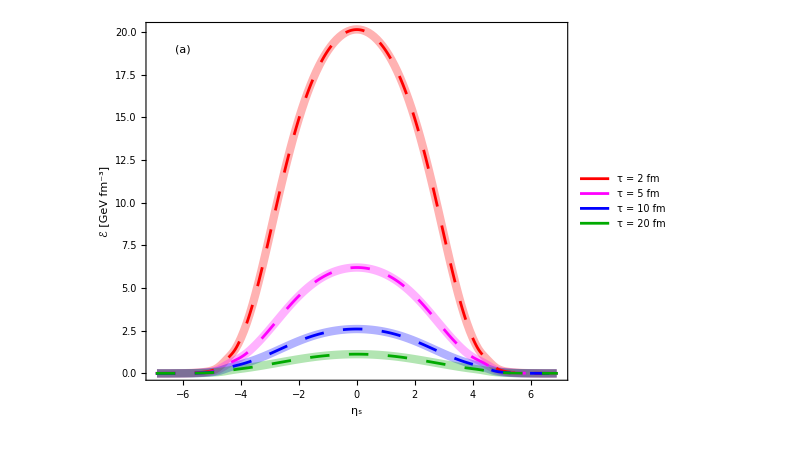

```mathematica
plot1=ListPlot[{e2,e5,e10,e20},PlotRange->{{-7,7},All},PlotStyle->{{AbsoluteThickness[6],Red,Opacity[0.3]},{AbsoluteThickness[6],Magenta,Opacity[0.3]},{AbsoluteThickness[6],Blue,Opacity[0.3]},{AbsoluteThickness[6],Darker[Green],Opacity[0.3]}},Axes->False,
Frame->True,FrameLabel->{"η_s","ℰ [GeV fm^-3]"},FrameStyle->Directive[AbsoluteThickness[1.1]],FrameTicksStyle->Thick,BaseStyle->{FontFamily->"Times",FontSize->30},ImageSize->600,AspectRatio->0.75,Joined->True,Epilog->Inset["(a)",{-6.0,19}]];
plot1n=ListPlot[{{1,0.197} #&/@e2n,{1,0.197} #&/@e5n,{1,0.197} #&/@e10n,{1,0.197} #&/@e20n},PlotRange->{{-7,7},All},PlotStyle->{{AbsoluteThickness[2],Red,Dashing[Large]},{AbsoluteThickness[2],Magenta,Dashing[Large]},{AbsoluteThickness[2],Blue,Dashing[Large]},{AbsoluteThickness[2],Darker[Green],Dashing[Large]}},Axes->False,Joined->True,Frame->True,FrameLabel->{"η_s","ℰ [GeV fm^-3]"},FrameStyle->Directive[AbsoluteThickness[1.1]],FrameTicksStyle->Thick,PlotLegends->Placed[LineLegend[{{"τ = 2   fm","τ = 5   fm","τ = 10 fm","τ = 20 fm"}},LabelStyle-> {FontSize->22,FontFamily->"Times"},LegendMarkerSize->{{30,10}}],{.85,0.70}],BaseStyle->{FontFamily->"Times",FontSize->30},ImageSize->600,AspectRatio->0.75];
plotE=Show[plot1,plot1n]
```

### Baryon Density

```mathematica
rhob1=Import[root<>"/tests/music-test/rhob_baryon_init.dat"];
rhob2=Import[root<>"/tests/music-test/rhob_baryon_t2.dat"];
rhob5=Import[root<>"/tests/music-test/rhob_baryon_t5.dat"];
rhob10=Import[root<>"/tests/music-test/rhob_baryon_t10.dat"];
rhob20=Import[root<>"/tests/music-test/rhob_baryon_t20.dat"];
```

```mathematica
rhob1ndata=Import[root<>"/output/rhob_1.000.dat"];
rhob1n=rhob1ndata[[All,{3,4}]];
rhob2ndata=Import[root<>"/output/rhob_2.000.dat"];
rhob2n=rhob2ndata[[All,{3,4}]];
rhob5ndata=Import[root<>"/output/rhob_5.000.dat"];
rhob5n=rhob5ndata[[All,{3,4}]];
rhob10ndata=Import[root<>"/output/rhob_10.000.dat"];
rhob10n=rhob10ndata[[All,{3,4}]];
rhob20ndata=Import[root<>"/output/rhob_20.000.dat"];
rhob20n=rhob20ndata[[All,{3,4}]];
```

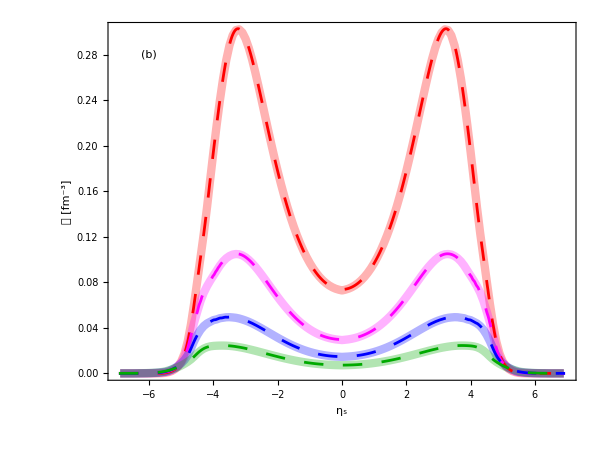

```mathematica
plot1=ListPlot[{rhob2,rhob5,rhob10,rhob20},PlotRange->{{-7,7},All},PlotStyle->{{AbsoluteThickness[6],Red,Opacity[0.3]},{AbsoluteThickness[6],Magenta,Opacity[0.3]},{AbsoluteThickness[6],Blue,Opacity[0.3]},{AbsoluteThickness[6],Darker[Green],Opacity[0.3]}},Axes->False,
Frame->True,FrameLabel->{"η_s","𝒩 [fm^-3]"},FrameStyle->Directive[AbsoluteThickness[1.1]],FrameTicksStyle->Thick,BaseStyle->{FontFamily->"Times",FontSize->30},ImageSize->600,AspectRatio->0.75,Joined->True,Epilog->Inset["(b)",{-6.0,0.28}]];
plot1n=ListPlot[{rhob2n,rhob5n,rhob10n,rhob20n},PlotRange->{{-7,7},All},PlotStyle->{{AbsoluteThickness[2],Red,Dashing[Large]},{AbsoluteThickness[2],Magenta,Dashing[Large]},{AbsoluteThickness[2],Blue,Dashing[Large]},{AbsoluteThickness[2],Darker[Green],Dashing[Large]}},Joined->True,Axes->False,Frame->True,FrameLabel->{"η_s","𝒩 [fm^-3]"},FrameStyle->Directive[AbsoluteThickness[1.1]],FrameTicksStyle->Thick,BaseStyle->{FontFamily->"Times",FontSize->30},ImageSize->600,AspectRatio->0.75];
plotN=Show[plot1,plot1n]
```

Test plots

```mathematica
Export["musictest_e.pdf",plotc,ImageResolution->200]
```

musictest_e.pdf

```mathematica
Export["musictest_rhob.pdf",plotc,ImageResolution->200]
```

musictest_rhob.pdf

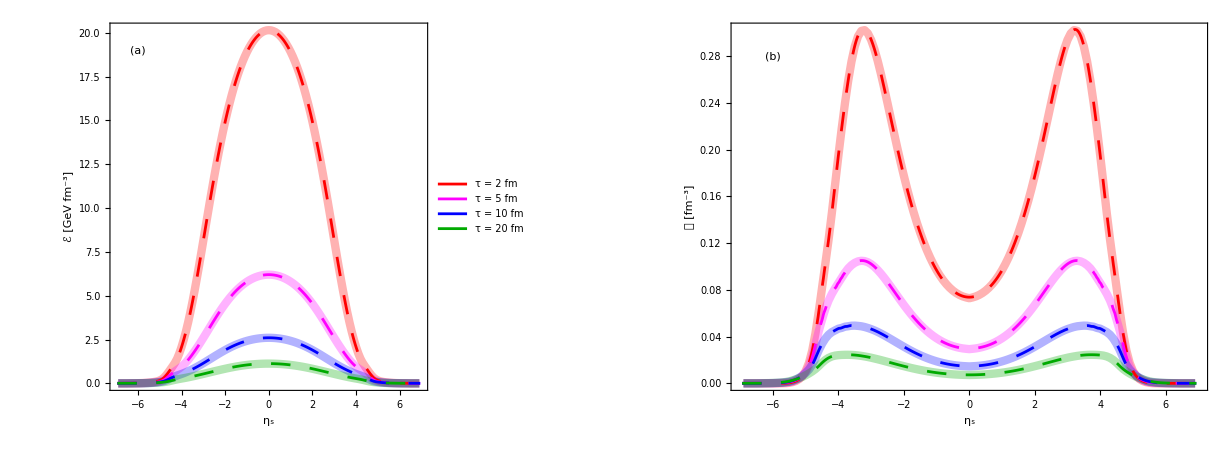

```mathematica
musicplot=GraphicsGrid[{{plotE,plotN}},Spacings->{10, 0}]
```

```mathematica
Export["Music_test.pdf",musicplot,ImageResolution->200]
```

Music_test.pdf